# Upwind Petrov-Galerkin method for convection dominated problems

One dimensional model problem:
This is simple one dimensional problem which demonstrates the motivation behind upwind methods.

```mathematica
Clear[x,T,ϕ];
```

```mathematica
DSolve[u  ϕ'[x] == k ϕ''[x],ϕ[x],x]
```

{{ϕ[x]→0.025 ⅇ^(40. x) C[1]+C[2]}}

Solution to the differential equation is given by:

```mathematica
u =20; L= 1; k=.5;
Pe = u L/k;
Φ[x_]:= (1-Exp[Pe *x/L])/(1-Exp[Pe]);
```

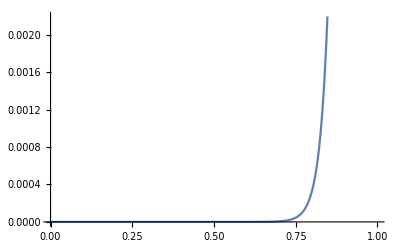

```mathematica
Plot[Φ[x],{x,0,1}]
```

Analytical solution for one dimensional case :

```mathematica
T[x_]:= (Exp[u L/k]-Exp[u / k x])/(Exp[u L/k]-1)
```

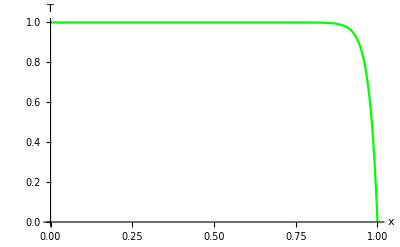

```mathematica
exact = Plot[T[x],{x,0,1},AxesLabel->{"x","T"},PlotPoints->200,PlotStyle->{Green},PlotRange->All]
```

Solution using simple hat functions:

```mathematica
h=1/8;

ϕ1[x_]:= Piecewise[{{1-x/h,0≤ x≤ h},{0,_}}];
ϕ2[x_]:= Piecewise[{{x/h,0≤ x≤ h},{2-x/h,h≤ x ≤2h}}];
ϕ3[x_]:= Piecewise[{{x/h-1,h≤ x≤ 2h},{3-x/h,2h<=x ≤3h}}];
ϕ4[x_]:= Piecewise[{{x/h-2,2h≤ x≤ 3h},{4-x/h,3h<=x ≤4h}}];
ϕ5[x_]:= Piecewise[{{x/h-3,3h≤ x≤ 4h},{5-x/h,4h<=x ≤5h}}];
ϕ6[x_]:= Piecewise[{{x/h-4,4h≤ x≤ 5h},{6-x/h,5h<=x ≤6h}}];
ϕ7[x_]:= Piecewise[{{x/h-5,5h≤ x≤ 6h},{7-x/h,6h<=x ≤7h}}];
ϕ8[x_]:= Piecewise[{{x/h-6,6h≤ x≤ 7h},{8-x/h,7h<=x ≤8h}}];
```

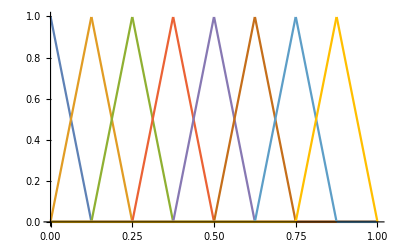

```mathematica
Plot[{ϕ1[x],ϕ2[x],ϕ3[x],ϕ4[x],ϕ5[x],ϕ6[x],ϕ7[x],ϕ8[x]},{x,0,1},PlotRange->All]
```

The boundary conditions:
T(0) = Ta 
and
-K dT/dx + h(T(L)-T_∞) = 0

We are solving K T = F using the Galerkin approach:

```mathematica
Q = 0.0; Clear[x];
ϕ = {ϕ1[x],ϕ2[x],ϕ3[x],ϕ4[x],ϕ5[x],ϕ6[x],ϕ7[x],ϕ8[x]};
F =Integrate[Q ϕ,{x,0,1}]; F[[1]]=1;
```

Conductivity matrix is given by:
K = ∫k dϕ_i/dx dϕ_j/dx

```mathematica
dϕ = D[ϕ,{x}];
K=k*Outer[Times,dϕ,dϕ];
```

```mathematica
Kint = Integrate[K,{x,0,1}]
```

{{4.,-4.,0.,0.,0.,0.,0.,0.},{-4.,8.,-4.,0.,0.,0.,0.,0.},{0.,-4.,8.,-4.,0.,0.,0.,0.},{0.,0.,-4.,8.,-4.,0.,0.,0.},{0.,0.,0.,-4.,8.,-4.,0.,0.},{0.,0.,0.,0.,-4.,8.,-4.,0.},{0.,0.,0.,0.,0.,-4.,8.,-4.},{0.,0.,0.,0.,0.,0.,-4.,8.}}

Additional advection term is given by:
U = ∫ρc u ϕ dT/dx dx

```mathematica
U=u Outer[Times,ϕ,dϕ];
Uint = Integrate[U,{x,0,1}]
```

{{-10,10,0,0,0,0,0,0},{-10,0,10,0,0,0,0,0},{0,-10,0,10,0,0,0,0},{0,0,-10,0,10,0,0,0},{0,0,0,-10,0,10,0,0},{0,0,0,0,-10,0,10,0},{0,0,0,0,0,-10,0,10},{0,0,0,0,0,0,-10,0}}

The final equation to satisfy is given as:
(K+U) T = F

```mathematica
M = Kint+Uint;
M[[1,All]]=0; M[[1,1]]=1; (*seting boundary conditions*)
```

```mathematica
Tsol= Inverse[M].F
```

{1.,1.0038,0.994936,1.01561,0.967365,1.07995,0.817257,1.4302}

```mathematica
Kint+Uint
```

{{-6.,6.,0.,0.,0.,0.,0.,0.},{-14.,8.,6.,0.,0.,0.,0.,0.},{0.,-14.,8.,6.,0.,0.,0.,0.},{0.,0.,-14.,8.,6.,0.,0.,0.},{0.,0.,0.,-14.,8.,6.,0.,0.},{0.,0.,0.,0.,-14.,8.,6.,0.},{0.,0.,0.,0.,0.,-14.,8.,6.},{0.,0.,0.,0.,0.,0.,-14.,8.}}

```mathematica
F
```

{1,0.,0.,0.,0.,0.,0.,0.}

```mathematica
xp={0,h,2h,3h,4h,5h,6h,7h,8h}; Tsol=Join[Tsol,{0}]
```

{1.,1.0038,0.994936,1.01561,0.967365,1.07995,0.817257,1.4302,0}

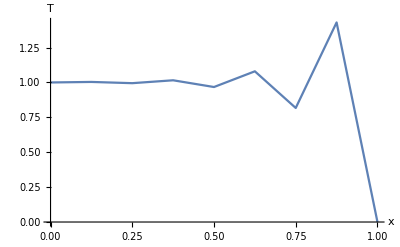

```mathematica
GM=ListLinePlot[Partition[Riffle[xp,Tsol],2],PlotRange->All,AxesLabel->{"x","T"},
AxesStyle->Arrowheads[{0,0.05}]]
```

For the upwind scheme we are using Petrov - Galerkin method:

```mathematica
γ = u/k;
β =Coth[γ/2]-2/γ;
W1[x_]:=ϕ1[x]+β h/2 dϕ[[1]];
W2[x_]:=ϕ2[x]+β h/2 dϕ[[2]];
W3[x_]:= ϕ3[x]+β h/2 dϕ[[3]];
W4[x_]:= ϕ4[x]+β h/2 dϕ[[4]];
W5[x_]:= ϕ5[x]+β h/2 dϕ[[5]];
W6[x_]:= ϕ6[x]+β h/2 dϕ[[6]];
W7[x_]:= ϕ7[x]+β h/2 dϕ[[7]];
W8[x_]:= ϕ8[x]+β h/2 dϕ[[8]];
```

Similar like before we are solving the equations:
(K+U) T = F, however now the equations are solved with different W - weighting functions.

```mathematica
W={W1[x],W2[x],W3[x],W4[x],W5[x],W6[x],W7[x],W8[x]};
FW = Integrate[Q W,{x,0,1}]; FW[[1]] =1;
```

The conductivity matrix is given by:
KW = ∫kdW/dx dϕ/dxdx

```mathematica
dW = D[W,{x}];
```

```mathematica
KW=k*Outer[Times,dW,dϕ];
```

```mathematica
KWint = Integrate[KW,{x,0,1}]
```

{{4.,-4.,0.,0.,0.,0.,0.,0.},{-4.,8.,-4.,0.,0.,0.,0.,0.},{0.,-4.,8.,-4.,0.,0.,0.,0.},{0.,0.,-4.,8.,-4.,0.,0.,0.},{0.,0.,0.,-4.,8.,-4.,0.,0.},{0.,0.,0.,0.,-4.,8.,-4.,0.},{0.,0.,0.,0.,0.,-4.,8.,-4.},{0.,0.,0.,0.,0.,0.,-4.,8.}}

Additional advection term is given by:
UW = ∫ρc u W dT/dx dx= ∫ρcu Wdϕ/dxⅆx

```mathematica
UW = u Outer[Times,W,dϕ];
UWint = Integrate[UW,{x,0,1}]
```

{{-0.5,0.5,0.,0.,0.,0.,0.,0.},{-19.5,19.,0.5,0.,0.,0.,0.,0.},{0.,-19.5,19.,0.5,0.,0.,0.,0.},{0.,0.,-19.5,19.,0.5,0.,0.,0.},{0.,0.,0.,-19.5,19.,0.5,0.,0.},{0.,0.,0.,0.,-19.5,19.,0.5,0.},{0.,0.,0.,0.,0.,-19.5,19.,0.5},{0.,0.,0.,0.,0.,0.,-19.5,19.}}

```mathematica
Mint = KWint + UWint;
```

```mathematica
Mint[[1,All]]=0; Mint[[1,1]]=1; (*seting boundary conditions*)
```

```mathematica
TWsol= Inverse[Mint].FW
```

{1.,0.999999,0.999989,0.999927,0.999508,0.996697,0.977818,0.851064}

```mathematica
xw={0,h,2h,3h,4h,5h,6h,7h,8h}; TWsol=Join[TWsol,{0}]
```

{1.,0.999999,0.999989,0.999927,0.999508,0.996697,0.977818,0.851064,0}

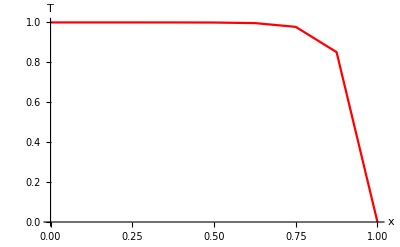

```mathematica
PG=ListLinePlot[Partition[Riffle[xw,TWsol],2],PlotRange->All,AxesLabel->{"x","T"},
AxesStyle->Arrowheads[{0,0.05}],PlotStyle->{Red},PlotRangePadding->Scaled[.08]]
```

Now we are comparing the exact solution with two numerical methods, Petrov-Galerkin and 
Galerkin method of obtaining FEM solutions. The Petrov-Galerkin method is obviously better
than Galerkin method for convection dominated problems.

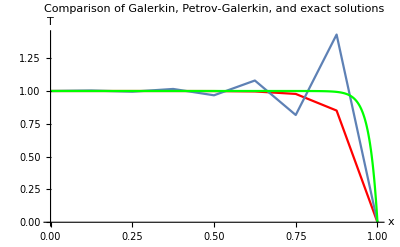

```mathematica
Show[{PG,GM,exact},PlotRange->All,PlotLabel->"Comparison of Galerkin, Petrov-Galerkin, and exact solutions"]
```